iteration1:root=1.5

iteration2:root=1.25

iteration3:root=1.375

iteration4:root=1.4375

iteration5:root=1.40625

iteration6:root=1.42188

iteration7:root=1.41406

iteration8:root=1.41797

iteration9:root=1.41602

iteration10:root=1.41504

1.41504

{1.5,1.25,1.375,1.4375,1.40625,1.42188,1.41406,1.41797,1.41602,1.41504}

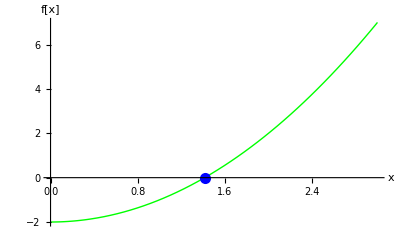

```mathematica
ClearAll;
f[x_]:=x^2-2;
a=1;
b=2;
e=0.001;
i=0; (*shomarande*)
clist={};
While[Abs[b-a]>e,i++;
c=(a+b)/2;
AppendTo[clist,N[c]];
Print["iteration",i,":root=",N[c]];
If[f[a]*f[c]<0,b=c,a=c];];
Print[N[c]] (*akharin rishe ro mide*)
(*nokte:ta n=10 rafte va dar n=8 ghat nakarde chon ta do ragham ashar ya 10^-2 gerd konim, degat dorost darmiad. yani do tay akhar ro kam konim yeki mishe*)
Print[clist]
Plot[f[x],{x,0,3},
GridLines->{{c},None},
GridLinesStyle->Directive[Blue,Dashed],
PlotStyle->{Green,Thick},
AxesLabel->{"x","f[x]"},
Epilog->{Blue,PointSize[0.02],Point[{c,f[c]}]}]
(*GridLines->{{c},0}     
GridLinesStyle->Directive[Blue,Dashed]   style GridLinesee ke neveshtim
PlotStyle->{Green,Thick}  style tabeee ke plotesh ro neveshtim
AxesLabel->{"x","f[x]"}     name mehvarha
Epilog->{Blue,PointSize[0.02]     fasele khotot mehvar va oon noghte ro abee karde
Point[{c,f[c]}]    mokhtasat rishe
*)
```